## Equilibrium calculation

```mathematica
A[α_,γ_]:=(1-γ)/(α γ);
k[α_,γ_,r_]:=(r+1)/(A[α,γ] (r-1)+r)-1;
```

```mathematica
q2=3;q1=2;
```

#### Type 1 conformists

```mathematica
β=2;α=0.8;
eqtype1conform[r_,α_,β_,γ_]:=If[γ<=0.38,1,1/(k[α,γ,r]^(1/β)+1)];
stable1[r_,α_,β_,γ_]:=0;
stable2[r_,α_,β_,γ_]:=If[γ≥0.38,1];
```

```mathematica
type1confdata=Import[NotebookDirectory[]<>"type1conf.csv","CSV"];
```

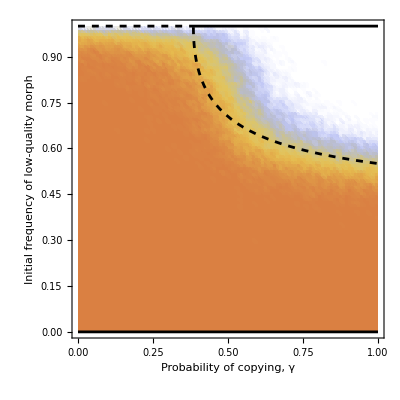

```mathematica
Show[ListDensityPlot[type1confdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype1conform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{-0.05,1.05},{-0.05,1.05}},PlotStyle->Directive[Dashed,Black,Thickness[0.005]],Frame->True,AspectRatio->1],
Plot[{stable1[q2/q1,α,β,γ],stable2[q2/q1,α,β,γ]},{γ,0,1},PlotRange->{{-0.05,1.05},{-0.05,1.05}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 1 anticonformists

```mathematica
α=2.8;β=-2;
```

```mathematica
eqtype1anticonform[r_,α_,β_,γ_]:=If[γ<=0.15,0,1/(k[α,γ,r]^(1/β)+1)];
unstable1[r_,α_,β_,γ_]:=1;
unstable2[r_,α_,β_,γ_]:=If[γ<=0.15,None,0]
```

```mathematica
type1anticonfdata=Import[NotebookDirectory[]<>"typeI_anticonformist_b-2/out.csv","CSV"];
```

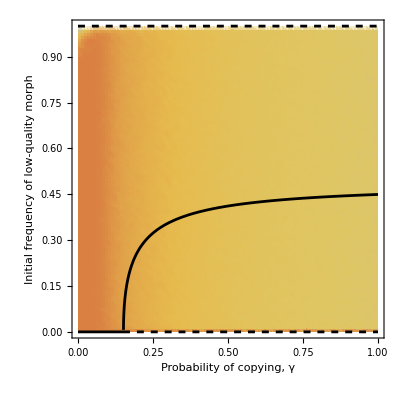

```mathematica
Show[ListDensityPlot[type1anticonfdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype1anticonform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1],
Plot[{unstable1[q2/q1,α,β,γ],unstable2[q2/q1,α,β,γ]},{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Dashed,Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 2 conformists

```mathematica
α=0.6;f=0.83;
```

```mathematica
eqtype2conform[r_,α_,β_,γ_]:=If[γ<0.45,1,If[0.45<γ&&γ<0.514,(1/(k[α,γ,r]+1)-f)/(1-f),If[γ≥0.515,0.5,None]]]
stable1[γ_]:=0;
stable2[γ_]:=If[0.45<γ,1];
```

```mathematica
type2confdata=Import[NotebookDirectory[]<>"typeII_conformist_f1.2/out.csv","CSV"];
```

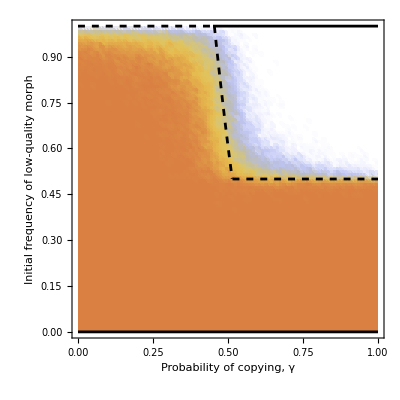

```mathematica
Show[ListDensityPlot[type2confdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype2conform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Dashed,Black,Thickness[0.005]],Frame->True,AspectRatio->1],
Plot[{stable1[γ],stable2[γ]},{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

#### Type 2 anticonformists

```mathematica
α=1.1;f=0.83;
```

```mathematica
eqtype2anticonform[r_,α_,β_,γ_]:=If[γ<0.3655,0,If[γ≥0.3655,0.5,None(*(1/(k[α,γ,r]+1)-f)/(1-f)*)]];
unstable1[γ_]:=1
unstable2[γ_]:=If[γ>0.3655,0,None]
```

```mathematica
type2anticonfdata=Import[NotebookDirectory[]<>"typeII_anticonformist_f1.2/out.csv","CSV"];
```

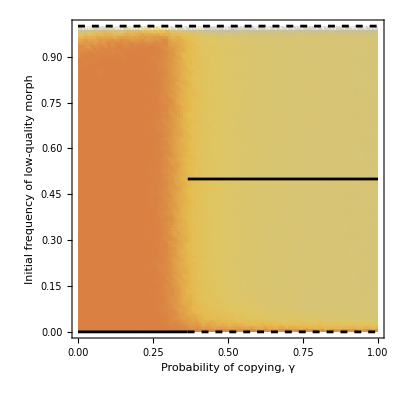

```mathematica
Show[ListDensityPlot[type2anticonfdata⟦2;;⟧,PlotRange->All,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Equilibrium frequency of low-quality morph",LabelStyle->{FontFamily->"Calibri"}],Above],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Initial frequency of low-quality morph",FontFamily->"Calibri",18]},ColorFunction->"BeachColors"],
Plot[eqtype2anticonform[q2/q1,α,β,γ],{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Black,Thickness[0.005]],Frame->True,AspectRatio->1],
Plot[{unstable1[γ],unstable2[γ]},{γ,0,1},PlotRange->{{0,1},{0,1}},PlotStyle->Directive[Dashed,Black,Thickness[0.005]],Frame->True,AspectRatio->1]]
```

Figure 2 e comes from the Figure SI weak calculation